```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
R=1;
L=1;
```

```mathematica
k[m_,n_]:= BesselJZero[m,n]/R;
```

```mathematica
Ez[r_,θ_,z_,m_,n_,p_]:=BesselJ[m,k[m,n]*r]* Cos[m θ] Cos[(p π z)/L];
```

```mathematica
zyl r[x_,y_,z_]:= Sqrt[x^2+y^2];
zyl θ[x_,y_,z_]:=ArcTan[x,y];
zyl z[x_,y_,z_]:=z;
```

```mathematica
offset = 0.0;
ColorFunc[z_]:=ColorData["LightTemperatureMap","ColorFunction"][offset+(1.0-offset)*z]
```

```mathematica
max[z_,m_,n_,p_]:=FindMaxValue[
{Ez[zyl r[x,y,z], zyl θ[x,y,z], zyl z[x,y,z],m,n,p],
{x,y}∈Disk[{0,0},1]},{x,y}];
```

```mathematica
plt[z_,m_,n_,p_]:=DensityPlot[Ez[zyl r[x,y,z], zyl θ[x,y,z], zyl z[x,y,z],m,n,p],{x,y}∈Disk[{0,0},1],Epilog->{Thick,Circle[]},PlotTheme->"Scientific",PlotRange->{-max[z,m,n,p],max[z,m,n,p]},ColorFunction->ColorFunc,Mesh->None,PlotPoints->40,FrameLabel->{"x","y"},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"E_z"]];
```

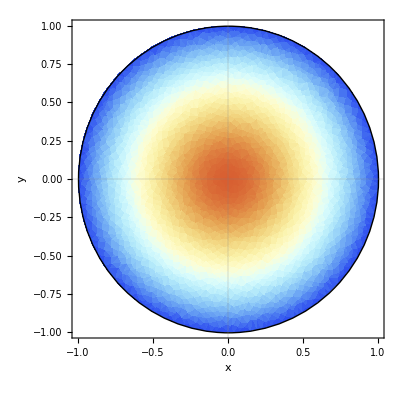

```mathematica
plt 1=plt[0.5,0,1,0]
```

```mathematica
Export["plot.pdf", plt 1,"AllowRasterization"->True, ImageSize->360,ImageResolution->600];
```

```mathematica
?PlotRange
```

PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot.

```mathematica
?ColorFunctionScaling
```

ColorFunctionScaling is an option for graphics functions that specifies whether arguments supplied to a color function should be scaled to lie between 0 and 1.

```mathematica
?RGBColor
```

RGBColor[red,green,blue] is a graphics directive specifying that objects that follow are to be displayed in the color given. 
RGBColor[r,g,b,a] specifies opacity a. 
RGBColor[string] evaluates to a normal RGBColor object.

```mathematica
ColorData["LightTemperatureMap","ColorFunction"][0.8]
```

RGBColor[0.9336260000000001, 0.7795129999999999, 0.44584699999999994]